# 补充资料【SU(2)超自由度光的可视化】

## FormFunction

```mathematica
FormFunction[{"x"->"Number","y"->"Number"},#x+#y&]
```

FormFunction[]

x和y是两个Field的变量名，在f中要用这两个变量进行数据处理，f就是按下submit激活的处理函数

f的形式：不能直接写为#+#2&，要在#后面跟上变量名，即x或y

```mathematica
TabView[{"参数式"->"x=A_xsin(ω_xt+δ_x) | y=sin(t) | 0≤t≤2 π\n\nω_x: horizontal angular frequency\nδ_x: horizontal angular phase\nA_x: horizontal amplitude"}]//TraditionalForm
```

1

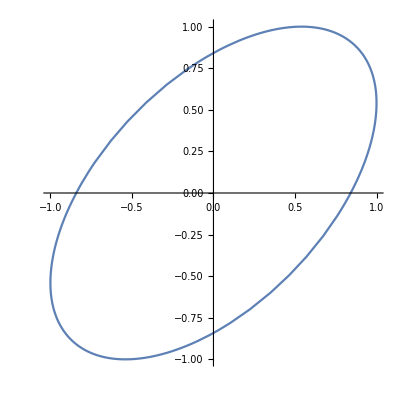

```mathematica
FormFunction[{{"Ax","A_x: horizontal angular frequency"}->"Number"->1,{"ωx","ω_x: horizontal angular phase"}->"Number"->1,{"δx","δ_x: horizontal amplitude"}->"Number"->1},ParametricPlot[{#Ax Sin[#ωx t+#δx],Sin[t]},{t,0,2π}]&,AppearanceRules-><|"Title"->"Lissajous Curve","Description"->"Enter A_x, ω_x and δ_x to visulize the curve"|>][]
```